```mathematica
ClearAll["Global`*"]
NotebookSave[]
Get["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Function.m"];
```

Distribution Parameters

```mathematica
rm=0.06;
rs=0.001;
sigmam=0.2;
sigmas=0.01;
S0m=44.;
S0s=.1;
```

Set Parameters

```mathematica
Num=1000;
M=50000;
callput="Put";
n=12.;
T=1.;
k=40.;
```

```mathematica
distrib={rdist,sigmadist,S0dist}={NormalDistribution[rm,rs],NormalDistribution[sigmam,sigmas],NormalDistribution[S0m,S0s]};
```

```mathematica
matrix=Table[distrib,{i,1,Num}];
```

```mathematica
MatRand1=Map[RandomVariate,matrix,{2}];
MatRand2=Map[RandomVariate,matrix,{2}];
```

```mathematica
(*Simul[M,callput,n,T,K,r,sigma,S0]*)
```

```mathematica
(*Param=Table[{M,callput,If[Mod[i-1,Num*3]≥Num*2,nm+ns,If[Mod[i-1,Num*3]≥Num,nm,nm-ns]],If[Mod[i-1,Num*9]≥Num*6,Tm+Ts,If[Mod[i-1,Num*9]≥Num*3,Tm,Tm-Ts]],
If[Mod[i-1,Num*27]≥Num*18,Km+Ks,If[Mod[i-1,Num*27]≥Num*9,Km,Km-Ks]]},{i,1,Num*27}];*)
```

```mathematica
Param=Table[{M,callput,n,T,k},{i,1,Num}];(*non-random parameters*)
```

```mathematica
MatA=Join[Param,MatRand1,2];
MatB=Join[Param,MatRand2,2];
```

```mathematica
For[i=Dimensions[Param][[2]]+1;VMat={},i≤Dimensions[MatA][[2]],i++,tmp=MatB;tmp[[All,i]]=MatA[[All,i]];AppendTo[VMat,tmp]]
```

```mathematica
DateList[]
```

{2017,11,19,14,15,9.2285879}

```mathematica
fA=ParallelTable[Simul@@MatA[[it3]],{it3,1,Num}];//AbsoluteTiming
```

{5925.57,Null}

```mathematica
DateList[]
```

{2017,11,19,15,53,54.8428939}

```mathematica
fB=ParallelTable[Simul@@MatB[[it4]],{it4,1,Num}];//AbsoluteTiming
```

{5957.54,Null}

```mathematica
DateList[]
```

{2017,11,19,17,33,12.409913}

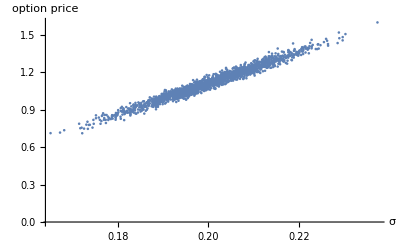

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}]
```

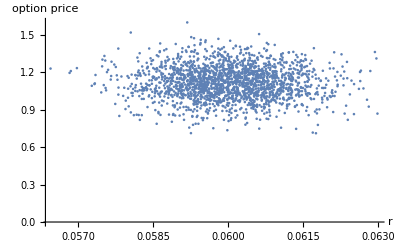

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]
```

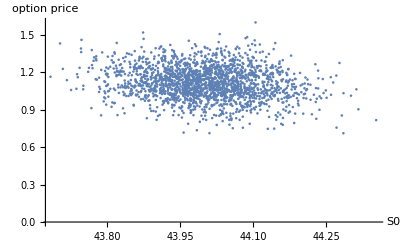

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}]
```

```mathematica
Monitor[For[it2=1;fVA={},it2<=Dimensions[VMat][[1]],it2++,tmp=ParallelTable[Simul@@VMat[[it2,it1]],{it1,1,Num}];AppendTo[fVA,tmp]],ProgressIndicator[it2,{1,Dimensions[VMat][[1]]}]];//AbsoluteTiming
```

{18034.5,Null}

```mathematica
DateList[]
```

{2017,11,19,22,33,47.5231932}

```mathematica
(*For[x=1;Var={},x≤Dimensions[fVA][[1]],x++,tmp=1/Num*Sum[fB[[w]]*(fVA[[x,w]]-fA[[w]]),{w,1,Num}];AppendTo[Var,tmp]]*)
```

```mathematica
For[x=1;Var1={},x≤Dimensions[fVA][[1]],x++,tmp=(1/Num*Sum[fA[[i]]*fVA[[x,i]],{i,Num}]-(1/Num*Sum[fA[[i]],{i,Num}])^2)/(1/Num*Sum[fA[[i]]*fA[[i]],{i,Num}]-(1/Num*Sum[fA[[i]],{i,Num}])^2);AppendTo[Var1,tmp]]
```

```mathematica
Var1
```

{0.0100703,0.970767,0.0224938}

```mathematica
For[x=1;Var2={},x≤Dimensions[fVA][[1]],x++,tmp=1/Num*Sum[fA[[w]]*(fVA[[x,w]]-fB[[w]]),{w,1,Num}];AppendTo[Var2,tmp]]
```

```mathematica
Var2/Total[Var2,2]
```

{-0.0111321,1.00907,0.00206091}

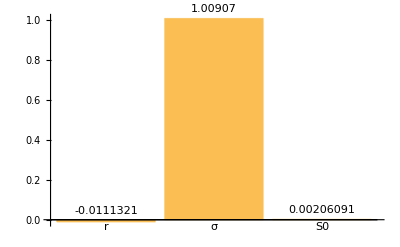

```mathematica
BarChart[Var2/Total[Var2,2],ChartLabels->{"r","σ","S0"},LabelingFunction->Above]
```

```mathematica
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatA3.m",MatA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatB3.m",MatB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fA3.m",fA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fB3.m",fB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fVA3.m",fVA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\Param3.m",Param[[1]]];
```

```mathematica
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\sigma3.eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}],"eps"];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\r3.eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\S03.eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}],"eps"];
```

```mathematica
NotebookSave[]
```